```mathematica
ClearAll["Global`*"]
```

```mathematica
dx = x(a11 (x-xs) + a12 (y-ys) + b1 (x^2 - xs^2) + b2 (x y - xs ys) + b3 (y^2 - ys^2))
```

x (a11 (x-xs)+b1 (x^2-xs^2)+a12 (y-ys)+b2 (x y-xs ys)+b3 (y^2-ys^2))

```mathematica
dy = y(a12 (x-xs) + a22 (y-ys) + b2 (x^2 - xs^2) + b3 (x y - xs ys) + b4 (y^2 - ys^2))
```

y (a12 (x-xs)+b2 (x^2-xs^2)+a22 (y-ys)+b3 (x y-xs ys)+b4 (y^2-ys^2))

```mathematica
A = {{a11,a12},{a12,a22}}
```

{{a11,a12},{a12,a22}}

```mathematica
B={{{b1, b2/2},{b2/2,b3}},{{b2,b3/2},{b3/2,b4}}}
```

{{{b1,b2/2},{b2/2,b3}},{{b2,b3/2},{b3/2,b4}}}

```mathematica
z = {x,y}
```

{x,y}

```mathematica
zs={xs,ys}
```

{xs,ys}

```mathematica
B[[1]]
```

{{b1,b2/2},{b2/2,b3}}

```mathematica
Pars = {a11->-9,a22->-9,a12->-1,b2->-1/4,b3->-1/4,b4->0,b1->0,xs->1,ys->1}
```

{a11→-9,a22→-9,a12→-1,b2→-1/4,b3→-1/4,b4→0,b1→0,xs→1,ys→1}

```mathematica
B[[1]]/.Pars
```

{{0,-1/8},{-1/8,-1/4}}

```mathematica
B[[2]]/.Pars
```

{{-1/4,-1/8},{-1/8,0}}

```mathematica
dZ=Table[z[[i]](Sum[A[[i,j]](z[[j]]-zs[[j]]),{j,1,2}]+Sum[B[[i,j,k]](z[[j]]z[[k]]-zs[[j]] zs[[k]]),{j,1,2},{k,1,2}]),{i,1,2}]
```

{x (a11 (x-xs)+b1 (x^2-xs^2)+a12 (y-ys)+b2 (x y-xs ys)+b3 (y^2-ys^2)),y (a12 (x-xs)+b2 (x^2-xs^2)+a22 (y-ys)+b3 (x y-xs ys)+b4 (y^2-ys^2))}

```mathematica
dZ-{dx,dy}
```

{0,0}

Compute growth rates

```mathematica
R=Table[(Sum[A[[i,j]](-zs[[j]]),{j,1,2}]+Sum[B[[i,j,k]](-zs[[j]] zs[[k]]),{j,1,2},{k,1,2}]),{i,1,2}]/.Pars
```

{21/2,21/2}

```mathematica
V= Collect[FullSimplify[Sum[R[[i]](z[[i]]-zs[[i]]),{i,1,2}]+(1/2)z.A.z-(1/2)zs.A.zs+(1/3)Sum[z[[i]]z.B[[i]].z,{i,1,2}]-(1/3)Sum[zs[[i]]zs.B[[i]].zs,{i,1,2}]]/.Pars,{x^3,y^3,x^2y , y^2 x, x^2,y^2,x,y},FullSimplify]
```

-32/3+x^2 (-9/2-y/6)+(21 y)/2-(9 y^2)/2+x (21/2-y-y^2/6)

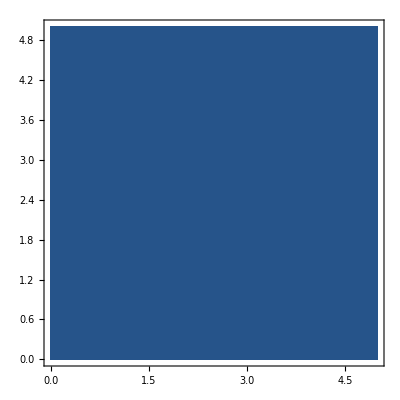

```mathematica
ContourPlot[Sign[V],{x,0,5},{y,0,5}]
```

```mathematica
V/.{x->2,y->2}
```

-34/3

```mathematica
dZ2=FullSimplify[dZ/.Pars]
```

{-1/4 x (-42+y (4+y)+x (36+y)),-1/4 y (x (4+x+y)+6 (-7+6 y))}

```mathematica
g = Table[Sum[A[[i,j]]+Sum[B[[i,j,k]](z[[k]]+zs[[k]]),{k,1,2}],{j,1,2}]/.{xs->s,ys->s},{i,1,2}]
```

{a11+a12+b1 (s+x)+1/2 b2 (s+x)+1/2 b2 (s+y)+b3 (s+y),a12+a22+b2 (s+x)+1/2 b3 (s+x)+1/2 b3 (s+y)+b4 (s+y)}

```mathematica
g= {γ1 + γ2 (x+xs)+γ3 (y + ys),γ4 + γ5 (x+xs)+γ6 (y + ys)}/.Pars
```

{γ1+(1+x) γ2+(1+y) γ3,γ4+(1+x) γ5+(1+y) γ6}

```mathematica
gs=g/.{x->xs,y->ys}/.Pars
```

{γ1+2 γ2+2 γ3,γ4+2 γ5+2 γ6}

```mathematica
W = α (x - xs - xs Log[x/xs])+ α (y - ys - ys Log[y/ys]) + β (g[[1]]-gs[[1]]-gs[[1]]Log[g[[1]]/gs[[1]]])+β (g[[2]]-gs[[2]]-gs[[2]]Log[g[[2]]/gs[[2]]])/.Pars
```

α (-1+x-Log[x])+α (-1+y-Log[y])+β (-2 γ2+(1+x) γ2-2 γ3+(1+y) γ3-(γ1+2 γ2+2 γ3) Log[(γ1+(1+x) γ2+(1+y) γ3)/(γ1+2 γ2+2 γ3)])+β (-2 γ5+(1+x) γ5-2 γ6+(1+y) γ6-(γ4+2 γ5+2 γ6) Log[(γ4+(1+x) γ5+(1+y) γ6)/(γ4+2 γ5+2 γ6)])

```mathematica
Collect[D[W,x]dZ2[[1]]+D[W,y]dZ2[[2]]/.Pars,{y^3,x^3},FullSimplify]
```

-1/4 x (-42+y (4+y)+x (36+y)) ((1-1/x) α+β (γ2-(γ2 (γ1+2 γ2+2 γ3))/(γ1+(1+x) γ2+(1+y) γ3))+β (γ5-(γ5 (γ4+2 γ5+2 γ6))/(γ4+(1+x) γ5+(1+y) γ6)))-1/4 y (x (4+x+y)+6 (-7+6 y)) ((1-1/y) α+β (γ3-(γ3 (γ1+2 γ2+2 γ3))/(γ1+(1+x) γ2+(1+y) γ3))+β (γ6-(γ6 (γ4+2 γ5+2 γ6))/(γ4+(1+x) γ5+(1+y) γ6)))